### canonical grid generation

#### vector

```mathematica
SinFunction[k_,sA_,shift_]:=sA bW Sin[2 Pi k n+shift]
```

```mathematica
n=7;
res=500;
r=1/3;
sAV=0.1;
sSV=Pi/2;
sCol=White;
bCol=Black;
hOn=True;
vOn=True;
```

```mathematica
GenerateGrid[n_,res_,r_,sAV_,sSV_,sAH_,sSH_,sCol_,bCol_,hOn_,vOn_]:=Module[
{sNL,bNL,sW,bW,sNH,bNH,sNV,bNV,hCoords,vCoords,hWidthComponents,vWidthComponents,verticalStreets,horizontalStreets,hShift,vShift,shrink,crossings,gridPoints},
sNL=0;bNL=0;sW=r/((1+r) n);bW=1/((1+r) n);sNH=RandomVariate[UniformDistribution[{1-sNL,1+sNL}],n+1];bNH=RandomVariate[UniformDistribution[{1-bNL,1+bNL}],n];sNV=RandomVariate[UniformDistribution[{1-sNL,1+sNL}],n+1];bNV=RandomVariate[UniformDistribution[{1-bNL,1+bNL}],n];hCoords=Table[(sW Total[sNH⟦1;;i-1⟧]+bW Total[bNH⟦1;;i-1⟧]+1/2 sW (sNH⟦i⟧-sNH⟦1⟧))/(sW Total[sNH]+bW Total[bNH]-1/2 sW (sNH⟦1⟧+sNH⟦n⟧)),{i,1,n+1}];vCoords=Table[(sW Total[sNV⟦1;;i-1⟧]+bW Total[bNV⟦1;;i-1⟧]+1/2 sW (sNV⟦i⟧-sNV⟦1⟧))/(sW Total[sNV]+bW Total[bNV]-1/2 sW (sNV⟦1⟧+sNV⟦n⟧)),{i,1,n+1}];hWidthComponents=Table[sW sNH⟦i⟧,{i,1,n+1}];vWidthComponents=Table[sW sNV⟦i⟧,{i,1,n+1}];verticalStreets=Table[(#1+{hCoords⟦i⟧,0.5}&)/@(#1-{hCoords⟦i⟧,0.5}&)/@Join[Table[{hCoords⟦i⟧+0.5 hWidthComponents⟦i⟧+SinFunction[k,sAV,sSV],k},{k,0,1,1/res}],Reverse[Table[{hCoords⟦i⟧-0.5 hWidthComponents⟦i⟧+SinFunction[k,sAV,sSV],k},{k,0,1,1/res}]]],{i,1,n+1}];horizontalStreets=Table[(#1+{0.5,vCoords⟦i⟧}&)/@(#1-{0.5,vCoords⟦i⟧}&)/@Join[Table[{k,vCoords⟦i⟧+0.5 vWidthComponents⟦i⟧-SinFunction[k,sAH,sSH]},{k,0,1,1/res}],Reverse[Table[{k,vCoords⟦i⟧-0.5 vWidthComponents⟦i⟧-SinFunction[k,sAH,sSH]},{k,0,1,1/res}]]],{i,1,n+1}];hShift=1/2 (Max[horizontalStreets]-1-Abs[Min[horizontalStreets]]);vShift=1/2 (Max[verticalStreets]-1-Abs[Min[verticalStreets]]);

shrink=1/Max[Max[horizontalStreets]-Min[horizontalStreets]-hShift,Max[verticalStreets]-Min[verticalStreets]-hShift];shrink=1;

crossings=Table[Table[If[i≠1&&j≠1&&i≠n+1&&j≠n+1,shrink {hCoords⟦i⟧-vShift-0.5,vCoords⟦j⟧-hShift-0.5},{0,0}],{j,1,n+1}],{i,1,n+1}];gridPoints=If[hOn,If[vOn,shrink Join[((#1+{-0.5,-0.5}&)/@#1&)/@(horizontalStreets-hShift),((#1+{-0.5,-0.5}&)/@#1&)/@(verticalStreets-vShift)],shrink ((#1+{-0.5,-0.5}&)/@#1&)/@(horizontalStreets-hShift)],If[vOn,shrink ((#1+{-0.5,-0.5}&)/@#1&)/@(verticalStreets-vShift),{}]];

Graphics[{
bCol,Rectangle[{-0.6,-0.6},{0.6,0.6}],
sCol,Polygon/@gridPoints
},ImageSize->{500,500},AspectRatio->1]
]
```

#### raster

```mathematica
MinPos[list_]:=Flatten[Position[list,Min[list]]][[1]]
DistFunction[pos_]:=Min[Map[EuclideanDistance[pos,#]&,pixelCoords]]
IllusionFunction[d_,hsp_,ab_,min_,max_]:=1-G[d,hsp,ab,min,max]
F[d_,hsp_,ab_]:=1/(1+Exp[ ab(d- hsp)])
G[d_,hsp_,ab_,min_,max_]:=(F[d,hsp,ab]-F[1,hsp,ab])(max-min)/(F[0,hsp,ab]-F[1,hsp,ab])+min
G2[F_,dist_,min_,max_]:=(F[dist]-F[1])(max-min)/(F[0]-F[1])+min
```

```mathematica
sW//N
```

0.047619

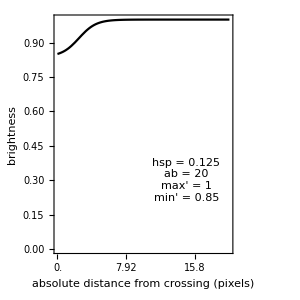
-Graphics--Graphics--Graphics-

```mathematica
n=7;
r=1/3;
approxSize=200;

hsp=0.125;
ab=20;
min=0;
max=0.15;

bW=1/(n+r+n r);
sW=r bW;
coords=Table[0.5sW+(i-1)(sW+bW),{i,1,n+1}];

possibleSizes=DeleteCases[
Table[
If[(n+1)Round[sW pixelSize]+n Round[bW pixelSize]==pixelSize,pixelSize]
,{pixelSize,approxSize-2n,approxSize+2n}]
,Null];

pixelSize=possibleSizes[[MinPos[
Map[
Abs[approxSize-#]&,
possibleSizes
]]]];

pixelCoords =Flatten[ Table[Table[
If[i==3&&j==3,
{-100,-100},
{Round[coords[[i]] pixelSize,0.5],Round[coords[[j]] pixelSize,0.5]}
]
,{j,2,n}],{i,2,n}],1];

maxPossibleDistance=Sqrt[2Power[pixelSize(sW+bW)/2,2]];

gridMatrix1=Table[Table[
If[
Total[Table[If[Abs[i pixelSize-0.5-coords[[k]] pixelSize]<pixelSize sW/2,1,0],{k,1,Length[coords]}]]==1 ||
Total[Table[If[Abs[j pixelSize-0.5-coords[[k]] pixelSize]<pixelSize sW/2,1,0],{k,1,Length[coords]}]]==1 ,
1,
0
]
,{j,1/pixelSize,1,1/pixelSize}],{i,1/pixelSize,1,1/pixelSize}];
gridMatrix2=Table[Table[
If[
Total[Table[If[Abs[i pixelSize-0.5-coords[[k]] pixelSize]<pixelSize sW/2,1,0],{k,1,Length[coords]}]]==1 ||
Total[Table[If[Abs[j pixelSize-0.5-coords[[k]] pixelSize]<pixelSize sW/2,1,0],{k,1,Length[coords]}]]==1 ,
If[
DistFunction[{i pixelSize-0.5,j pixelSize-0.5}]≤maxPossibleDistance,
If[
DistFunction[{i pixelSize-0.5,j pixelSize-0.5}]≤ sW pixelSize 0.5 10 ,
IllusionFunction[
DistFunction[{i pixelSize-0.5,j pixelSize-0.5}]/maxPossibleDistance,
hsp,
ab,
min,
max
],
1
],
1
],
0
]
,{j,1/pixelSize,1,1/pixelSize}],{i,1/pixelSize,1,1/pixelSize}]; 
imSize=300;
gridImage=Row[{
Image[gridMatrix1,ImageSize->{imSize,imSize}],
Plot[
IllusionFunction[d,hsp,ab,min,max],{d,0,1},
PlotStyle->{Black,Thick},PlotRange->{{0,1},{0,1}},
LabelStyle->{Black,FontFamily->"Cambria",FontSize->14},
Frame->{{True,False},{True,True}},
FrameLabel->{{"brightness",None},{"absolute distance from crossing (pixels)","relative distance from crossing"}},
FrameTicks->{{Automatic,None},{Table[{i,NumberForm[i maxPossibleDistance,3]},{i,0,1,0.2}],Table[i,{i,0,1,0.2}]}},
Epilog->{
Black,FontFamily->"Cambria",FontSize->20,Text["hsp = "<>ToString[hsp]<>"\nab = "<>ToString[ab]<>"\nmax' = "<>ToString[1-min]<>"\nmin' = "<>ToString[1-max],{0.75,0.3}](*,
RGBColor[1,1,1,0.8],
EdgeForm[Black],
Rectangle[{0.1,0.2},{0.98,0.8}],
RGBColor[1,0,0,1],FontSize->60,Text["TraditionalForm`r",{0.55,0.5}]*)},
AspectRatio->1,ImageSize->{imSize,imSize}
],
Image[gridMatrix2,ImageSize->{imSize,imSize}]
}]
```

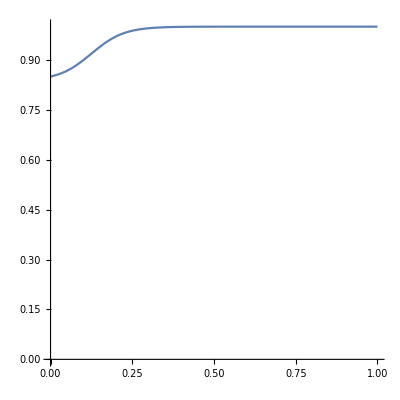

```mathematica
hsp=0.125;
ab=20;
min=0;
max=0.15;
Plot[
IllusionFunction[d,hsp,ab,min,max],
{d,0,1},PlotRange->{{0,1},{0,1}},AspectRatio->1
]
```

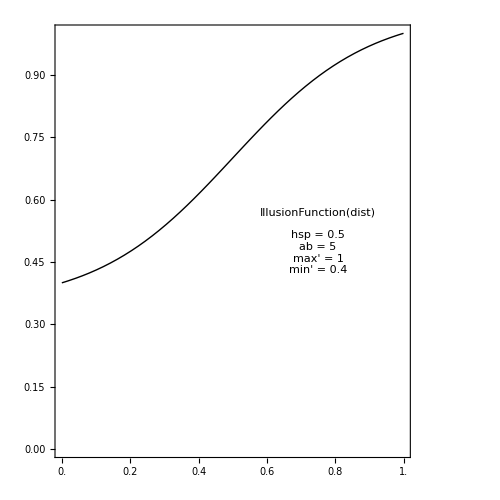

```mathematica
hsp=0.5;
ab=5;
min=0;
max=0.6;
iPlot=Plot[
1-G[d,hsp,ab,min,max],{d,0,1},
PlotStyle->{Black,Thick},PlotRange->{{0,1},{0,1}},
LabelStyle->{Black,FontFamily->"Cambria",FontSize->14},
Frame->{True,True},
FrameTicks->{{Automatic,None},{Table[i,{i,0,1,0.2}],None}},
Epilog->{Black,FontFamily->"Cambria",FontSize->20,Text["IllusionFunction(dist)\n\nhsp = "<>ToString[hsp]<>"\nab = "<>ToString[ab]<>"\nmax' = "<>ToString[1-min]<>"\nmin' = "<>ToString[1-max],{0.75,0.5}]},
AspectRatio->1,ImageSize->{500,500}
]
```

### isoluminant

#### kigyózó

```mathematica
isoluminantGrid=Style[ImageAdd[
Image[GenerateGrid[7,500,1/3,0,Pi/2,RGBColor[1,0,0],Black,True,True]],
Image[GenerateGrid[7,500,1/3,0.4,Pi/2,RGBColor[0,1,0],Black,False,True]]
],Antialiasing->False]
```

```mathematica
s1={0,243,33}/255;
b1={74,66,175}/255;
s2={197,158,81}/255;
b2={138,63,38}/255;
```

```mathematica
s1={0,249,17}/255;
b1={63,81,68}/255;
s2={172,155,79}/255;
b2={24,60,199}/255;
```

```mathematica
replacementRules={
{0,0,0}->b1,
{1,0,0}->s1,
{1,1,0}->s2,
{0,1,0}->b2
};
Table[
Export[
NotebookDirectory[]<>"\\iso2\\base.png",
Style[GenerateGrid[7,500,1/3,0,Pi/2,0,Pi/2,RGBColor[1,0,0],Black,True,True],Antialiasing->False]];
Export[
NotebookDirectory[]<>"\\iso2\\overlay.png",
Style[GenerateGrid[7,500,1/3,s,Pi/2,0,Pi/2,RGBColor[0,1,0],Black,False,True],Antialiasing->False]];
iso=ImageAdd[Import[NotebookDirectory[]<>"\\iso2\\base.png"],Import[NotebookDirectory[]<>"\\iso2\\overlay.png"]];
Export[NotebookDirectory[]<>"\\iso2\\overlaid_"<>ToString[s]<>".png",Image[Round[ImageData[iso]]/.replacementRules,ImageSize->{500,500}]];
,{s,0,0.01,0.05}];
```

```mathematica
isoluminantSeries1=Table[
Style[GenerateGrid[7,500,1/3,0,Pi/2,0,Pi/2,Blend[{RGBColor[s1],RGBColor[{0,0,1}]},blend],RGBColor[s2],True,True],Antialiasing->False],
{blend,0,1,0.1}];
```

```mathematica
isoluminantSeries2=Table[
Style[GenerateGrid[7,500,1/3,0,Pi/2,0,Pi/2,RGBColor[b1],Blend[{RGBColor[b2],RGBColor[{1,1,0}]},blend],True,True],Antialiasing->False],
{blend,0,1,0.1}];
```

```mathematica
contrastSeries=Table[
Style[GenerateGrid[7,500,1/3,0,Pi/2,0,Pi/2,RGBColor[1-blend,1-blend,1-blend],RGBColor[blend,blend,blend],True,True],Antialiasing->False],
{blend,0,0.5,0.05}];
```

```mathematica
Table[{
first=RandomInteger[{1,11}];
second=RandomInteger[{1,11}];
Export[
NotebookDirectory[]<>"\\design\\contrast\\"<>ToString[n]<>"_"<>ToString[first]<>"_"<>ToString[second]<>".png",
Row[{contrastSeries[[first]],contrastSeries[[second]]}]
]
},{n,1,10}]
```

{{C:\Users\marku\Documents\CEU\hermann grid\human\grid_isoluminant\\design\contrast\1_9_2.png},{C:\Users\marku\Documents\CEU\hermann grid\human\grid_isoluminant\\design\contrast\2_6_3.png},{C:\Users\marku\Documents\CEU\hermann grid\human\grid_isoluminant\\design\contrast\3_8_6.png},{C:\Users\marku\Documents\CEU\hermann grid\human\grid_isoluminant\\design\contrast\4_5_5.png},{C:\Users\marku\Documents\CEU\hermann grid\human\grid_isoluminant\\design\contrast\5_2_11.png},{C:\Users\marku\Documents\CEU\hermann grid\human\grid_isoluminant\\design\contrast\6_6_6.png},{C:\Users\marku\Documents\CEU\hermann grid\human\grid_isoluminant\\design\contrast\7_3_3.png},{C:\Users\marku\Documents\CEU\hermann grid\human\grid_isoluminant\\design\contrast\8_11_5.png},{C:\Users\marku\Documents\CEU\hermann grid\human\grid_isoluminant\\design\contrast\9_6_6.png},{C:\Users\marku\Documents\CEU\hermann grid\human\grid_isoluminant\\design\contrast\10_4_11.png}}

```mathematica
isoluminantSeries1
```